# Optimal Control of a 2D Cart

Brian Beckman
September 2025

## Abstract

Consider the problem of a cart that is free to slide on a frictionless, flat, level plane in 2 dimensions. We wish to control the cart via two thrusters so that it returns to the origin at zero velocity after any disturbance that accelerates it in the plane. This problem seems trivial, and optimal control might seem overkill for it. However, we intend later to balance a massive baton, free to move in two angular  directions, on the cart. Such a baton can be called an inverted spherical pendulum, or a 3D baton. Balancing a 3D baton on a 2D cart is much more challenging than balancing a 2D baton (free to move in one angular direction) on a 1D cart (free to move in one spatial dimension). That classic problem can be solved analytically. To my knowledge, balancing the 3D pendulum can only be numerically solved.

## Global Constants (Initialization Cells)

Rectangular basis vectors, e_1,e_2,e_3, origin o, acceleration of Earth’s gravity g in m/sec^2, a default plot range with padding, and a time range for numerical integration.

```mathematica
ClearAll[e1,e2,e3,o,g,plotRg,tLim];
e1={1,0,0};e2={0,1,0};e3={0,0,1};
o={0,0,0};
g=QuantityMagnitude@Quantity[-9.81,"kg m / s^2"];
plotRg=QuantityMagnitude@Quantity[{-1.25,1.25},"m"];
tLim=QuantityMagnitude@Quantity[200,"s"];
```

## State Space Form

Let the cart be a massive disc. We will not rotate it so rectangular shape would be distracting. Specify parameters via Wolfram’s Quantity, but save only the magnitudes for numerical purposes.

```mathematica
ClearAll[kartMass,kartRadius];
kartMass=QuantityMagnitude@Quantity[1,"kg"];
kartRadius=QuantityMagnitude@Quantity[0.1,"m"];
```

Let f be an external perturbation force. Our goal will be to compensate for this force with a control force u.

Let f be constant + sinusoidal in each of two directions, x and y. Represent f by a vector of the real parts of complex exponentials:

f(t)= Re [f_(0,x) + A_x e^(i(t/P_x+φ_x)), f_(0,y)+ A_y e^(i(t/P_y+φ_y))]ᵀ

where

f_(0,i∈{x,y}) are constant forces in the two Cartesian directions x and y

A_(i∈{x.y}) are the amplitudes of the sinusoidal forces in the two directions

P_(i∈{x,y}) are the periods of oscillations in the two directions

φ_(i∈{x,y}) are the starting phase angles of oscillations at time t=0

Pick some arbitrary concrete values for demonstration:

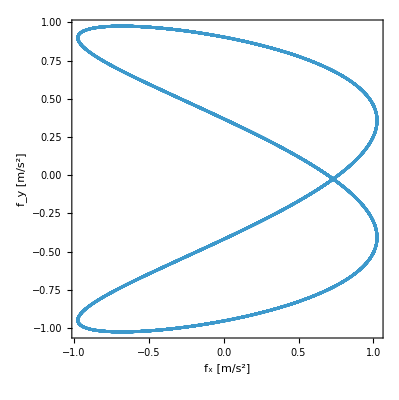

```mathematica
ClearAll[uX,uY,uZ,
fX,fY,fZ,
fXConst,fXAmplitude,fXPhase,fXPeriod,
fYConst,fYAmplitude,fYPhase,fYPeriod];
fXAmplitude=QuantityMagnitude@Quantity[1.,"kg m / s^2"];
fXPhase=105°//N;
fXPeriod=QuantityMagnitude@Quantity[0.125,"s"];
fXConst=QuantityMagnitude@Quantity[0.1/4,"kg m / s^2"];
fYAmplitude=QuantityMagnitude@Quantity[1.,"kg m / s^2"];
fYPhase=-15°//N;
fYPeriod=QuantityMagnitude@Quantity[0.25,"s"];
fYConst=QuantityMagnitude@Quantity[-0.1/4,"kg m / s^2"];
fX[t_]:=fXConst+fXAmplitude Re[ Exp[ⅈ (t/fXPeriod+fXPhase)]]
fY[t_]:=fYConst+fYAmplitude Re[ Exp[ⅈ( t/fYPeriod+fYPhase)]]
fZ[t_]:=g(* floor support force *)
ParametricPlot[{fX[t],fY[t]},{t,0,tLim/10},Frame->True,FrameLabel->{"f_x [m/s^2]","f_y [m/s^2]"}]
```

Let T and V be kinetic and potential energies of the free cart, without the forces f and u. From these, construct the Lagrangian in 3D Cartesian coordinates and the Euler-Lagrange equations of motion with f as the non-conservative forces on the right-hand sides. The following is idiomatic in the Wolfram language for computing the Euler-Lagrange equations.

```mathematica
ClearAll[kartT,kartV,kartX,kartY,kartZ];
kartT[{x_,y_,z_}]:=(1/2)kartMass(D[x,t]^2+D[y,t]^2+D[z,t]^2)
kartV[{x_,y_,z_}]:=kartMass g z
ClearAll[kartL,kartLeqns,Lcrds,Lvels,Lncnf];
kartL[{x_,y_,z_}]:=kartT[{x,y,z}]-kartV[{x,y,z}]
Lcrds={kartX[t],kartY[t],kartZ[t]};
Lvels=D[Lcrds,t];
kartL[{kartX[t],kartY[t],kartZ[t]}]
Lncnf={fX[t],fY[t],fZ[t]};(* non-conservative forces *)
kartLeqns=Flatten@MapThread[
{q,v,f}↦D[D[kartL[Lcrds],v],t]-D[kartL[Lcrds],q]==f,
{Lcrds,Lvels,Lncnf}]//FullSimplify
```

9.81 kartZ[t]+1/2 (kartX'[t]^2+kartY'[t]^2+kartZ'[t]^2)

{kartX''[t]==0.025+1. Re[ⅇ^(ⅈ (1.8326+8. t))],kartY''[t]==-0.025+1. Re[ⅇ^(ⅈ (-0.261799+4. t))],kartZ''[t]==0}

Set the initial conditions to be at rest at the origin of the coordinate frame:

```mathematica
ClearAll[kartInitials];
kartInitials={
kartX[0]==0,kartX'[0]==0,
kartY[0]==0,kartY'[0]==0,
kartZ[0]==0,kartZ'[0]==0}
```

{kartX[0]==0,kartX'[0]==0,kartY[0]==0,kartY'[0]==0,kartZ[0]==0,kartZ'[0]==0}

Solve the equations of motion numerically, without compensation force u, for the uncontrolled motion:

```mathematica
ClearAll[kartNum];
kartNum=NDSolve[kartLeqns~Join~kartInitials,Lcrds~Join~Lvels,{t,0,tLim}];
```

Plot 10 seconds worth of motion:

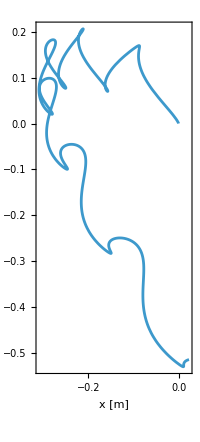

```mathematica
ParametricPlot[{kartX[t],kartY[t]}/.kartNum,{t,0,0.05tLim},Frame->True,FrameLabel->{"x [m]","y [m]"}]
```

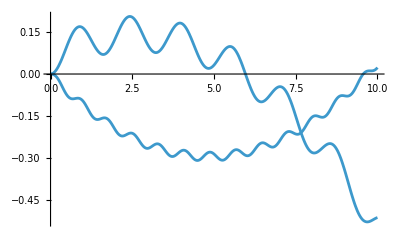

```mathematica
Plot[{kartX[t],kartY[t]}/.kartNum,{t,0,0.05tLim}]
```

## Visualization

Animate the motion of the cart and display its energy, which we can see fluctuating under the action of the perturbation force. There is a lot of code, here, but it’s mostly graphics machinery.

```mathematica
ClearAll[nfm,vfm,font,myFont];
myFont[color_,size_:18]:=Style[#,color,Bold,size,FontFamily->"Courier New"]&;
nfm[num_,dig_:10,dec_:4]:=ToString[NumberForm[Chop@num,{dig,dec}]];
vfm[vec_]:=ToString[NumberForm[#,{7,4},
NumberSigns->{"-"," "}, NumberPadding->{" ", "0"}]&/@Chop@vec];
font=myFont[Blue,12];
```

```mathematica
With[{epsilon=0.0001,h=1/15.,w=1/4.,vu=3.},
With[{ztxt=-1.5,xtxt=0,ytxt=-2,znl=0.3},
With[{kart=Cylinder[{o,{0,0,epsilon}},w],
floor=Polygon[{{-vu,-vu,0},{vu,-vu,0},{vu,vu,0},{-vu,vu,0}}],
axisLabelStyle=text↦Style[text,Red,Bold,18,FontFamily->"Courier New"],
thin={0,0,epsilon},s=2},
With[{},
Manipulate[DynamicModule[{},
Animate[
Module[{renderPos=o,kartPos,Tnum,Vnum},
renderPos=(kartX[t]/.kartNum[[1]]/.t->u) e1+(kartY[t]/.kartNum[[1]]/.t->u) e2;
kartPos[t_]:={kartX[t],kartY[t],kartZ[t]};
Tnum=(1/2)kartMass kartPos'[t].kartPos'[t]/.kartNum[[1]]/.t->u;
Vnum=kartMass g kartPos[t][[3]]/.kartNum[[1]]/.t->u;
Show[{Graphics3D[{
Text[font["t = "<>nfm@u<>
", E = "<>nfm@(Tnum+Vnum)],
{xtxt,ytxt,ztxt}],
Text[font["{δ_0,η_0} = "<>vfm@{δ0/°,η0/°}],{xtxt,ytxt,ztxt-znl}],
Text[font["{δ,η} = "<>vfm@{δx,ηx}],{xtxt,ytxt,ztxt-2znl}],
Text[font["c_s = "<>vfm@cs],{xtxt,ytxt,ztxt-3znl}],
{Yellow,Opacity[.3/4],floor},
{Green,Opacity[.6],Translate[kart,renderPos]}},
ImageSize->Large,Axes->True,AxesLabel->axisLabelStyle/@{"X","Y","Z"},
PlotRange->{{-vu,vu},{-vu,vu},{-vu,vu}}]}]],
{u,0,tL},AnimationRate->.5]],
{{δ0,10.°},0,90.°},{{η0,5.°},0,90.°},{{tL,tLim/10},0,tLim}]]]]]
```

## Optimal Control

## Coordinate System

What are good generalized coordinates and velocities for The spherical pendulum? Spherical coordinates have a singularity at the North pole, right where we want (in future notebooks) to control the baton. A better choice are pitch and cone roll (not axis roll!): co-latitude δ and angular displacement η at a clockwise right angle to the great-circle arc of co-latitude. These are spherical coordinates tipped over so the singularities are on the Equator, better than singularities at the North poles because the simulated baton—and its numerical integrators—will, with high likelihood, fly through these singularities, not linger at them.

## Dynamical Set-Up

### Center of mass (CM)

... in terms of a symbolic constant, c_z, the height of the CM in the body frame of the baton:

```mathematica
ClearAll[cm];
(cm[{δ_,η_}]:=RotationMatrix[-η,e1].RotationMatrix[δ,e2].{0,0,Subscript[c, z]});
cm[{δ,η}]//MatrixForm
```

(Sin[δ] c_z
Cos[δ] Sin[η] c_z
Cos[δ] Cos[η] c_z)

### z-Height

The potential energy depends only on the z-height, zh[δ,η], the third component of the CM as the baton rotates around the fixed spherical hinge point:

```mathematica
ClearAll[zh];
zh[{δ_,η_}]:=-cm[{δ,η}][[3]];
zh[{δ,η}]
```

-Cos[δ] Cos[η] c_z

### Symbolical and Numerical Forms

We’ll need symbolical and numerical functions for both potential and kinetic energy. The symbolical functions support Wolfram’s calculus with symbolical functions like δ[t], η[t], δ '[t], and η'[t], yielding the Euler-Lagrange equations of motion, and also Wolfram’s numerical integrators.^[15] The numerical energy functions support graphical demonstrations.

#### numRules

For numerical functions, we replace parametric functions δ[t], η[t], δ'[t],η'[t], with unbound symbols δ,Dδ,η,Dη. We also add numerical rule for the mass m and CM z-height:

```mathematica
ClearAll[numRules];
numRules={δ[t]->δ,η[t]->η,δ'[t]->Dδ,η'[t]->Dη,m->1,Subscript[c, z]->1.2};
```

### Potential Energy

Here are the symbolical and numerical potential-energy functions, with the acceleration of gravity, g, numerical in both cases because we treat it as a global constant:

```mathematica
ClearAll[Vnum,V];
V[{δ_,η_}]:=m g zh[{δ,η}];V[{δ,η}]
(* Notice not :=, SetDelayed, but =, Set *)
Vnum[{δ_,η_}]=((V[{δ,η}])/.numRules);
Vnum[{δ[t],η[t]}]
```

4.905 Cos[δ] Cos[η] c_z

5.886 Cos[δ[t]] Cos[η[t]]

### Kinetic Energy

#### Velocity Vector

The kinetic energy depends on the velocity vector, computed via the Wolfram D function:

```mathematica
ClearAll[v];
(v[{δ_,η_}]:=D[cm[{δ,η}],t]);
v[{δ[t],η[t]}]//FullSimplify//MatrixForm
```

(Cos[δ[t]] c_z δ'[t]
c_z (-Sin[δ[t]] Sin[η[t]] δ'[t]+Cos[δ[t]] Cos[η[t]] η'[t])
-c_z (Cos[η[t]] Sin[δ[t]] δ'[t]+Cos[δ[t]] Sin[η[t]] η'[t]))

Here are the symbolical and numerical kinetic-energy functions:

```mathematica
ClearAll[Tnum,T];
(T[{δ_,η_}]:=1/2 m v[{δ,η}].v[{δ,η}]);
T[{δ[t],η[t]}]//FullSimplify
(* hand-constructed, for checking *)
Tnum[{δ_,η_},{Dδ_,Dη_}]:=1/2(1.2)^2(Dδ^2+Cos[δ]^2 Dη^2);
Tnum[{δ_,η_},{Dδ_,Dη_}]:=1/2(1.2)^2(Dδ^2+(1/2(1+Cos[2δ]))Dη^2);
(* Set =, not SetDelayed := *)
Tnum[{δ_,η_},{Dδ_,Dη_}]=(T[{δ[t],η[t]}]/.numRules//FullSimplify);
Tnum[{δ,η},{Dδ,Dη}]
```

0.25 c_z^2 (1. δ'[t]^2+(0.5+0.5 Cos[2 δ[t]]) η'[t]^2)

0.36 Dδ^2+0.18 Dη^2+0.18 Dη^2 Cos[2 δ]

### Lagrangians

L is for the late-discretized solution. Lnum  is for the early-discretized Lagrangian, L_d.

```mathematica
ClearAll[Lnum,L];
(L[{δ_,η_}]:=T[{δ,η}]-V[{δ,η}]);L[{δ[t],η[t]}]//FullSimplify
Lnum[{δ_,η_},{Dδ_,Dη_}]:=Tnum[{δ,η},{Dδ,Dη}]-Vnum[{δ,η}];
Lnum[{δ,η},{Dδ,Dη}]
```

c_z (-4.905 Cos[δ[t]] Cos[η[t]]+c_z (0.25 δ'[t]^2+(0.125+0.125 Cos[2 δ[t]]) η'[t]^2))

0.36 Dδ^2+0.18 Dη^2+0.18 Dη^2 Cos[2 δ]-5.886 Cos[δ] Cos[η]

### Leqns

Wolfram has symbolical magic for the Euler-Lagrange equations. See Reference [15].

```mathematica
ClearAll[Leqns];
With[{Lcrds={δ[t],η[t]}},
With[{Lvels=D[Lcrds,t]},
With[{Lncnf={0,0}},(* non-conservative forces *)
Leqns=Flatten@MapThread[
{q,v,f}↦D[D[L[Lcrds],v],t]-D[L[Lcrds],q]==f,
{Lcrds,Lvels,Lncnf}]]]]//FullSimplify
```

{c_z (-19.62 Cos[η[t]] Sin[δ[t]]+c_z (1. Sin[2 δ[t]] η'[t]^2+2. δ''[t]))==0,Cos[δ[t]] c_z (-9.81 Sin[η[t]]+c_z (-2. Sin[δ[t]] δ'[t] η'[t]+1. Cos[δ[t]] η''[t]))==0}

#### State-Space Form

Differential equations in state-space form are first-order, thus easier for Wolfram to integrate. We get them by solving Leqns for δ''[t] and η''[t]:

```mathematica
ClearAll[stEqns];
stEqns=Equal@@@(Solve[Leqns,{δ''[t],η''[t]}]//FullSimplify//Chop//Part[#,1]&)
```

{δ''[t]==Sin[δ[t]] ((9.81 Cos[η[t]])/c_z-1. Cos[δ[t]] η'[t]^2),η''[t]==(9.81 Sec[δ[t]] Sin[η[t]])/c_z+2. Tan[δ[t]] δ'[t] η'[t]}

## Late Discretization: Numerical Solution of Continuous Equations

Solve the system for  tLim=200  simulated seconds (this time limit is the new feature of this notebook over its ancestor notebook, Reference 31); tLim is a new global constant for the rest of this notebook:

```mathematica
ClearAll[tLim,initialConditions,stSolns];
tLim=200;
initialConditions={δ[0]==10°,η[0]==5°,δ'[0]==0,η'[0]==0};
stSolns=NDSolve[Append[stEqns,initialConditions]/.{Subscript[c, z]->1.2},{δ[t],η[t],δ'[t],η'[t]},{t,0,tLim}]
```

{{δ[t]→InterpolatingFunction[…][t],η[t]→InterpolatingFunction[…][t],δ'[t]→InterpolatingFunction[…][t],η'[t]→InterpolatingFunction[…][t]}}

### Plot the Solutions

```mathematica
Manipulate[DynamicModule[{
ics={δ[0]==δ0,η[0]==η0,δ'[0]==0,η'[0]==0},δx,δDotx,ηx,ηDotx,flt},
δx=stSolns[[1,1,2]];δDotx=stSolns[[1,3,2]];ηx=stSolns[[1,2,2]];ηDotx=stSolns[[1,4,2]];
flt="δ_0 = "<>ToString[δ0]<>"°, η_0 = "<>ToString[η0]<>"°";
GraphicsGrid[{
{Plot[δx/°,{t,0,tL},FrameLabel->{{"δ [deg]",""},{"t [sec]",flt}},Frame->True],
Plot[δDotx/°,{t,0,tL},FrameLabel->{{"ⅆ_tδ [deg/sec]",""},{"t [sec]",flt}},Frame->True]},
{Plot[ηx/°,{t,0,tL},FrameLabel->{{"η [deg]",""},{"t [sec]",flt}},Frame->True],
Plot[ηDotx/°,{t,0,tL},FrameLabel->{{"ⅆ_tη [deg/sec]",""},{"t [sec]",flt}},Frame->True]}}]],
{{δ0,10.°},0.,90.°},{{η0,5.°},0,90.°},{{tL,tLim/10},0,tLim}]
```

### Animation

This is pretty convincing. Energy is well conserved. We’d only have to reboot it after a long time. If we were satisfied with an integrator that works only inside Wolfram, we’d be just about done. But we want an integrator we can code up in any programming language.

#### Graphical Support Routines

```mathematica
ClearAll[rig];
With[{l=1.2,mass=1.0,d=2.4,r=0.02},
With[{baton=Cylinder[{{0,0,-l},{0,0,+l}},r],
batonCenterBodyFrame={0,0,l}},
(* Immutable constant properties *)
rig["graphics primitives"]=baton;
rig["moment of inertia"]=
With[{Ib=mass*(MomentOfInertia[baton]/Volume[baton])},
With[{Ibi=Inverse@Ib},{Ib,Ibi}]];
rig["cb"]:=batonCenterBodyFrame;
rig["half length"]:=l;
rig["mass"]:=mass;
]];
```

```mathematica
ClearAll[jack];
jack[0,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,e1}],diameter]},
{Darker[Green],Arrow[Tube[{o,e2}],diameter]},
{Blue,Arrow[Tube[{o,e3}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,-e1}],diameter]},
{Magenta,Arrow[Tube[{o,-e2}],diameter]},
{Yellow,Arrow[Tube[{o,-e3}],diameter]}};
jack[rq_Quaternion,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,rv[rq,e1]}],diameter]},
{Darker[Green],Arrow[Tube[{o,rv[rq,e2]}],diameter]},
{Blue,Arrow[Tube[{o,rv[rq,e3]}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,rv[rq,-e1]}],diameter]},
{Magenta,Arrow[Tube[{o,rv[rq,-e2]}],diameter]},
{Yellow,Arrow[Tube[{o,rv[rq,-e3]}],diameter]}};
jack[ωHat_List,opacity_:0.1,diameter_:0.01]:={
Opacity[opacity],
{Red,Arrow[Tube[{o,ωHat.e1}],diameter]},
{Darker[Green],Arrow[Tube[{o,ωHat.e2}],diameter]},
{Blue,Arrow[Tube[{o,ωHat.e3}],diameter]},
{Lighter[Cyan],Arrow[Tube[{o,ωHat.-e1}],diameter]},
{Magenta,Arrow[Tube[{o,ωHat.-e2}],diameter]},
{Yellow,Arrow[Tube[{o,ωHat.-e3}],diameter]}};
```

```mathematica
ClearAll[nfm,vfm,font,myFont];
myFont[color_,size_:18]:=Style[#,color,Bold,size,FontFamily->"Courier New"]&;
nfm[num_,dig_:10,dec_:4]:=ToString[NumberForm[Chop@num,{dig,dec}]];
vfm[vec_]:=ToString[NumberForm[#,{7,4},
NumberSigns->{"-"," "}, NumberPadding->{" ", "0"}]&/@Chop@vec];
font=myFont[Blue,12];
```

```mathematica
With[{epsilon=0.0001,h=1/15.,w=1/4.,vu=3.},
With[{ztxt=-1.5,xtxt=0,ytxt=-2,znl=0.3},
With[{kart=Cuboid[{-w,-w,epsilon},{w,w,epsilon+h}],
floor=Polygon[{{-vu,-vu,0},{vu,-vu,0},{vu,vu,0},{-vu,vu,0}}],
axisLabelStyle=text↦Style[text,Red,Bold,18,FontFamily->"Courier New"],
cb=rig["cb"],thin={0,0,.0001},s=2,o={0,0,0}},
With[{c3=Cylinder[{o,thin},s cb[[3]]],b3=Sphere[o,s cb[[3]]],t3x=Tube[{-s cb[[3]] e2,s cb[[3]] e2},.01]},
Manipulate[DynamicModule[{
ics={δ[0]==δ0,η[0]==η0,δ'[0]==0,η'[0]==0},δx,Dδx,ηx,Dηx,flt},
δx=stSolns[[1,1,2]];Dδx=stSolns[[1,3,2]];ηx=stSolns[[1,2,2]];Dηx=stSolns[[1,4,2]];
Animate[
Module[{renderPos=o,cs,rotfn},
cs=RotationMatrix[-ηx/.t->u,e1].RotationMatrix[δx/.t->u,e2].cb;
renderPos=-cs[[1]]e1-cs[[2]]e2;
rotfn=RotationTransform[-ηx/.t->u,e1]@*RotationTransform[δx/.t->u,e2];
Show[{Graphics3D[{
Text[font["t = "<>nfm@u<>
", E = "<>nfm@(Tnum[{δx/.t->u,ηx/.t->u},{Dδx/.t->u,Dηx/.t->u}]+Vnum[{δx/.t->u,ηx/.t->u}])],
{xtxt,ytxt,ztxt}],
Text[font["{δ_0,η_0} = "<>vfm@{δ0/°,η0/°}],{xtxt,ytxt,ztxt-znl}],
Text[font["{δ,η} = "<>vfm@{(δx/.t->u)/°,(ηx/.t->u)/°}],{xtxt,ytxt,ztxt-2znl}],
Text[font["c_s = "<>vfm@cs],{xtxt,ytxt,ztxt-3znl}],
{Black,t3x},
{White,Opacity[.7/8],c3,b3,
GeometricTransformation[c3,RotationTransform[δx/.t->u,e2]]},
GeometricTransformation[jack[0],rotfn],
{Red,Sphere[cs,1/16.]},
{Yellow,Opacity[.3/4],floor},
{Green,Opacity[.6],Translate[kart,renderPos]},
{White,Opacity[.75],Translate[Translate[
GeometricTransformation[rig["graphics primitives"],rotfn],
cs],renderPos+(epsilon+h)e3]}},
ImageSize->Large,Axes->True,AxesLabel->axisLabelStyle/@{"X","Y","Z"},
PlotRange->{{-vu,vu},{-vu,vu},{-vu,vu}}],
ParametricPlot3D[RotationMatrix[-ha,e1].RotationMatrix[δx/.t->u,e2].cb,{ha,0,2π}]}]],
{u,0,tL},AnimationRate->.5]],
{{δ0,10.°},0,90.°},{{η0,5.°},0,90.°},{{tL,tLim/10},0,tLim}]]]]]
```

Part::partd: Part specification stSolns[[1,1,2]]
     is longer than depth of object.

Part::partd: Part specification stSolns[[1,3,2]]
     is longer than depth of object.

Part::partd: Part specification stSolns[[1,2,2]]
     is longer than depth of object.

General::stop: Further output of Part::partd
     will be suppressed during this calculation.

Part::partd: Part specification stSolns⟦1,1,2⟧ is longer than depth of object.

Part::partd: Part specification stSolns⟦1,3,2⟧ is longer than depth of object.

Part::partd: Part specification stSolns⟦1,2,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

## Early Discretization

Discretize the dynamical variables and the Lagrangian, itself, via Equation 7 of Reference [10]. First, a reminder:

```mathematica
??Lnum
```

Whereas LNum takes a coordinate tuple q and a velocity tuple q̇, the discrete Lagrangian L_d takes a pair of coordinate tuples: one, q_k, at time t_k, and another, q_(k+1), at time t_(k+1).

L_d is actually discretized action (units of energy × time), being the product of LNum (units of energy) and the finite (constant) time increment dt.

```mathematica
ClearAll[Ld,pk,pkp1,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,dt];
Ld[qk:{δk_,ηk_},qkp1:{δkp1_,ηkp1_},dt_]:=dt Lnum[1/2(qk+qkp1),1/dt(qkp1-qk)];
```

### Discrete Euler-Lagrange Equations

The discrete Euler-Lagrange equations, without generalized force terms, are

D_1 L_d(q_k,q_(k+1))+D_2 L_d(q_(k-1),q_k)=0

We comment-out the original calculations specifically to exhibit the results explicitly, writing d1ld for D_1 L_d and d2ld for D_2 L_d.

```mathematica
ClearAll[d1ld,d2ld];
(* Subscript[D, 1] Subscript[L, d](Subscript[q, k],Subscript[q, k+1]) *)
d1ld[{δk_,ηk_},{δkp1_,ηkp1_},dt_]:=
(* {D[Ld[{δk,ηk},{δkp1,ηkp1},dt],δk]//FullSimplify,
D[Ld[{δk,ηk},{δkp1,ηkp1},dt],ηk]//FullSimplify}, Evaluate in Place *)
{1/dt(-1.44(-δk+δkp1)+5.886 dt^2 Cos[(ηk+ηkp1)/2] Sin[(δk+δkp1)/2]-0.36 (ηk-ηkp1)^2 Sin[δk+δkp1]),
1/dt(0.72ηk-0.72ηkp1+(0.72ηk-0.72ηkp1) Cos[δk+δkp1]+5.886 dt^2 Cos[(δk+δkp1)/2] Sin[(ηk+ηkp1)/2])};
(* +Subscript[D, 2] Subscript[L, d](Subscript[q, k-1],Subscript[q, k]) *)
d2ld[{δkm1_,ηkm1_},{δk_,ηk_},dt_]:=
(* +{D[Ld[{δk,ηk},{δkp1,ηkp1},dt],δkp1]//FullSimplify,
D[Ld[{δk,ηk},{δkp1,ηkp1},dt],ηkp1]//FullSimplify}, Evaluate in Place *){1/dt(1.44 (δk-δkm1)+5.886 dt^2 Cos[(ηk+ηkm1)/2] Sin[(δk+δkm1)/2]-0.36 (ηk-ηkm1)^2 Sin[δk+δkm1]),1/dt(0.72 ηk-0.72 ηkm1+(0.72 ηk-0.72 ηkm1) Cos[δk+δkm1]+5.886 dt^2 Cos[(δk+δkm1)/2] Sin[(ηk+ηkm1)/2])};
```

### Numerical Solution for δ_1 and η_1

All we need is FindRoot, which we could replace with an explicit (faster?) Newton-Raphson solver in C, C++, Fortran, or Python, for instance. We bootstrap the integrator by taking the first two positions from the late-discretized solution.

We take 800000 samples with a time step of 1/4000=250μs—quite fine grained, specifically to show that DVI’s periodic energy noise obtains even for fine-grained time steps. Evaluating this expression takes several minutes, so we save screen shots of the results and mark cells not-evaluatable in the cell-properties menu of Wolfram’s notebook interface. Make the cells evaluatable if you wish to reproduce the results.

Notice that the angles are qualitatively the same as in late discretization, but show a growth in the envelope of the angles. This is unacceptable and undiagnosed.

```mathematica
tLim=200;
```

```mathematica
ClearAll[δt,ηt,dt,fh,δ0,η0,δ1,η1,tn,len,nvars,dsoln];
δt=stSolns[[1,1,2]];ηt=stSolns[[1,2,2]];
dt=1/4000;(* sec *)fh=1.0*dt;
δ0=δt/.{t->0};η0=ηt/.{t->0};
δ1=δt/.{t->dt};η1=ηt/.{t->dt};
tn= tLim; (* sec *)
len=tn/dt;
nvars=2;
dsoln=ConstantArray[0,{2nvars,len}];
dsoln[[1,1]]=δ0;dsoln[[2,1]]=η0;
dsoln[[1,2]]=δ1;dsoln[[2,2]]=η1;
Echo@Quiet@AbsoluteTiming@
For[j=2,j<len,j+=1,
Module[{pj,δkm1,ηkm1,δk,ηk,δkp1,ηkp1,r},
δkm1=dsoln[[1,j-1]];ηkm1=dsoln[[2,j-1]];
δk=dsoln[[1,j]];ηk=dsoln[[2,j]];
pj=d1ld[{δk,ηk},{δkp1,ηkp1},dt]+d2ld[{δkm1,ηkm1},{δk,ηk},dt];
r=FindRoot[pj,{{δkp1,δk},{ηkp1,ηk}}];
dsoln[[1;;2,j+1]]=r[[;;,2]];
dsoln[[3;;4,j+1]]=(dsoln[[1;;2,j+1]]-dsoln[[1;;2,j]])/fh;    ]];
ListLinePlot[dsoln[[1;;2,;;]],Frame->True,GridLines->Automatic,FrameLabel->{{"Angles",""},{"time step",{"Early-Discretized Angles versus Time"}}}]
```

{207.061,Null}

### Energies of Late Discretization

```mathematica
ClearAll[TnumFlat,VnumFlat];
TnumFlat[δ_,η_,dδ_,dη_]:=Tnum[{δ,η},{dδ,dη}];
VnumFlat[δ_,η_]:=Vnum[{δ,η}];
```

```mathematica
dδ=dsoln[[1]];
dη=dsoln[[2]];
dδDot=dsoln[[3]];
dηDot=dsoln[[4]];
dT=MapThread[TnumFlat,{dδ,dη,dδDot,dηDot}];
dV=MapThread[VnumFlat,{dδ,dη}];
dE=dT+dV;
mdE=Mean[dE];
headFrac=1;
nδ=Table[stSolns[[1,1,2]]/.t->u,{u,0dt,(len-1)/headFrac dt,dt}];
nδDot=Table[stSolns[[1,3,2]]/.t->u,{u,0dt,(len-1)/headFrac dt,dt}];
nη=Table[stSolns[[1,2,2]]/.t->u,{u,0dt,(len-1)/headFrac dt,dt}];
nηDot=Table[stSolns[[1,4,2]]/.t->u,{u,0dt,(len-1)/headFrac dt,dt}];
nT=MapThread[TnumFlat,{nδ,nη,nδDot,nηDot}];
nV=MapThread[VnumFlat,{nδ,nη}];
nE=nT+nV;
mnE=Mean[nE];
```

From the late-discretized solution, we calculate a mean energy of mnE = 11.5490. Energy slowly drifts in the fifth decimal place (sixth significant figure). However, we see that Wolfram occasionally corrects the error drift. That is one of the two primary discoveries of this notebook.

```mathematica
ListLinePlot[(nE-mnE), Frame->True,GridLines->Automatic,FrameLabel->{{"Energy",""},{"time step","Late-Discretized Energy versus Time"}}]
```

The late-discretized solution has a mean energy of 11.5486+/-0.014, differing from early-discretized energy in the 5-th figure and with a standard deviation consistent with that difference. The early-discretized solution has a periodic error of about that amplitude, about 1000 times larger than the standard deviation of the energy of the early-discretized solution. While the late-discretized solution has no discernible secular (long-term) trend, it has a visibly growing, even accelerating, periodic error. This is the second of the two major discoveries of this notebook. Diagnosis of this error awaits future work. As it stands, it is unacceptable.

```mathematica
ListLinePlot[{(nE-mnE)*1000,(dE-mdE)},Frame->True,GridLines->Automatic,FrameLabel->{{"Energy", ""},{"time step","Early-Discretized Energy and Late-Discretized Energy versus Time"}},PlotLegends->{"Late","Early"}]
```

## Conclusion

The early-discretized solution accumulates and loses energy. Remarkably, Wolfram’s integrators detect energy divergence and correct themselves, though opaquely and internally. That correction, coupled with their remarkable execution speed, makes the Wolfram integrators suitable for secular energy studies, though not for export to internal applications.

We see, again, that early discretization conserves energy in the mean much better than does late discretization. The periodic error of early discretization, though still acceptably small, is 1000 times greater than the secular error drift of late discretization. That periodic error, along with the slow execution speed of early discretization, renders it unpractical. However, it remains mathematically interesting and practically promising if it can be made fast enough and if the periodic noise can be diagnosed and mitigated.

## References

This is a list of general references on discrete variational dynamics and the background mathematics. Not all these references are cited directly in this notebook.

Jack B Kuipers, Quaternions and Rotation Sequences, Princeton University Press, 1999.

Jeongseok Lee, Karen Liu, Frank C. Park, Siddartha S. Srinivasa, A Linear-Time Variational Integrator for Multibody Systems, 2018, https://arxiv.org/abs/1609.02898

Ari Stern, Discrete Geometric Mechanics and Variational Integrators, 2006, http://ddg.cs.columbia.edu/SIGGRAPH06/stern-siggraph-talk.pdf.

Ethan Eade, Lie Groups for 2D and 3D Transformations, 2017, http://ethaneade.com/lie.pdf.

NIST: Digital Library of Mathematical Functions, https://dlmf.nist.gov.

Brian C. Hall, Lie Groups, Lie Algebras, and Representations, Second Edition, 2015, Springer.

Guangyu Liu, Modeling, stabilizing control and trajectory tracking of a spherical inverted pendulum, PhD thesis, 2007, University of Melbourne, 
https://minerva-access.unimelb.edu.au/handle/11343/37225.

Wikipedia, Tennis-Racket Theorem, https://en.wikipedia.org/wiki/Tennis_racket_theorem.

Marin Kobilarov, Keenan Crane, Mathieu Desbrun, Lie Group Integrators for Animation and Control of Vehicles, 2009 (?).

Ari Stern, Mathieu Desbrun, Discrete Geometric Mechanics for Variational Time Integrators, 2006 (http://www.geometry.caltech.edu/pubs/SD06.pdf).

Kenth Engø, On The BCH Formula in 𝔰𝔬(3), https://www.researchgate.net/profile/Kenth_Engo-Monsen2/publication/233591614_On _the _BCH-formula_in _so3/links/004635199177f69467000000/On-the-BCH-formula-in-so3.pdf.

Alexander Van-Brunt, Max Visser, Explicit Baker-Campbell-Hausdorff formulae for some specific Lie algebras, https://arxiv.org/pdf/1505.04505.pdf.

Wikipedia, Baker-Campbell-Hausdorff Formula, https://en.wikipedia.org/wiki/Baker% E2 %80 %93 Campbell % E2 %80 %93 Hausdorff_formula.

Jerrold E. Marsden, Tudor S. Ratiu, Introduction to Mechanics and Symmetry, Second Edition, 2002

Moylan, Andrew, Stabilized Inverted Pendulum, https://blog.wolfram.com/2011/01/19/stabilized-inverted-pendulum/, and Stabilized n-Link Pendulum, https://blog.wolfram.com/2011/03/01/stabilized-n-link-pendulum/

Paul R. Halmos, Naive Set Theory, 2015.

David Lovelock and Hanno Rund, Tensors, Differential Forms, and Variational Principles, 1975.

Ralph Abraham and Jerrold E. Marsden, Foundations of Mechanics: 2nd Edition, 1980.

Taeyoung Lee, Melvin Leok, N. Harris McClamroch, Discrete Control Systems, https://arxiv.org/abs/0705.3868.

Taeyoung Lee, Melvin Leok, N. Harris McClamroch, Global Formulations of Lagrangian and Hamiltonian Mechanics on Manifolds, Springer, https://a.co/d/0lTbL9t.

Tristan Needham, Visual Differential Geometry and Forms, https://a.co/d/9hoKekz.

xAct, Efficient tensor computer algebra for the Wolfram Language, http://xact.es/index.html.

Blanco, Jose-Luis, A tutorial on SE(3) transformation parameterizations and on-manifold optimization, Technical Report #012010, Universidad de Malaga (https://jinyongjeong.github.io/Download/SE3/jlblanco2010geometry3d_techrep.pdf).

Marsden and West has exhaustive treatment of Noether’s Theorem (http://www.cds.caltech.edu/~marsden/bib/2001/09-MaWe2001/MaWe2001.pdf).

Maxime Tournier, Notes on Lie Groups, https://maxime-tournier.github.io/notes/lie-groups.html.

John Baez, Javier P. Muniain, Gauge Fields, Knots and Gravity, (https://a.co/d/jdRnOU0).

F. C. Park, J. E. Bobrow, S. R. Ploen, A Lie Group Formulation of Robot Dynamics.

George W. Hart, Multidimensional Analysis, https://a.co/d/8c5RqOX

Evandro Bernardes, Stephane Viollet, Quaternion to Euler angles conversion: A direct, general and computationally efficient method, PLoS ONE 17(11) e0276302

Linear Quadratic Regulator, from Underactuated Robotics, https://underactuated.mit.edu/lqr.html

Brian Beckman, Discrete variational spherical pendulum: free motion, https://community.wolfram.com/groups/-/m/t/3359568